```mathematica
Clear[measureDistance];

measureDistance[image_]:=Manipulate[DynamicModule[{pts={},x1=Null,x2=Null,ΔX,X1,X2,g,myRound},myRound[x_]:=Round[1000*x]/1000//N;
(*Begins the column with all the content of the manipulate*)Column[{(*Begin LocatorPane*)Dynamic@LocatorPane[Union[Dynamic[pts]],Dynamic@Show[{Image[image,ImageSize->size],Graphics[{color,AbsoluteThickness[lineThickness],Opacity[opacity],Line[Union[pts]]}]}],LocatorAutoCreate->True,(*Begin Locator appearance*)Appearance->If[whiteLocatorRing,Graphics[{{color,AbsoluteThickness[thickness],Circle[{0,0},radius+thickness/2]},{White,AbsoluteThickness[thickness],Circle[{0,0},radius]}},ImageSize->10],Graphics[{{color,AbsoluteThickness[thickness],Circle[{0,0},radius+thickness/2]}},ImageSize->10]](*End Locator appearance*)],(*End LocatorPane*)(*Begin of the block of InputFields*)Row[{Style["\!\(\*SubscriptBox[\(x\), \(1\)]\):"],InputField[Dynamic[x1],FieldHint->"Type  \!\(\*SubscriptBox[\(x\), \(1\)]\)",FieldSize->7,FieldHintStyle->{Red}],Spacer[20],Style["   \!\(\*SubscriptBox[\(x\), \(2\)]\):"],InputField[Dynamic[x2],FieldHint->"Type  \!\(\*SubscriptBox[\(x\), \(2\)]\)",FieldSize->7,FieldHintStyle->{Red}],(*Begin button "Memorize scale X"*)Spacer[30],Button["Memorize scale",X1=Min[Transpose[myRound/@Union[pts]][[1]]];
X2=Max[Transpose[myRound/@Union[pts]][[1]]];
ΔX=X2-X1;](*End of button "Memorize scale X"*)}],(*End of the block of InputFields and button*)Spacer[20],(*Begin button "Make the list of the curve's points"*)Button[Style["Pick up the locators coordinates and calculate the distance between them",Bold],g[{a_,b_}]:={(x1*X2-x2*X1)/ΔX+a/ΔX*Abs[x2-x1],(x1*X2-x2*X1)/ΔX+b/ΔX*Abs[x2-x1]};
Clear[poinTs,diStance];
poinTs=Map[myRound,Map[g,pts]];
diStance=poinTs//Differences//Norm],(*End of button "Make the list..."*)Row[{Style["Locators coordinates:      ",14,Blue,Bold],InputField[Dynamic[poinTs]]}],Spacer[10],Row[{Style["The inter-locator distance: ",14,Blue,Bold],InputField[Dynamic[diStance]]}]},Alignment->Center](*End of column with all the content of the manipulate*)],(*End of the DynamicModule*)(*The massive of sliders begins*)Column[{Row[{Control[{whiteLocatorRing,{True,False}}],Spacer[50]}],Row[{Spacer[32.35],Control[{{size,450},300,800}],Spacer[38.5],Control[{{opacity,0.5},0,1}]}],Row[{Spacer[10.],Control[{{thickness,1},0.5,5}],Spacer[13.65],Control[{{lineThickness,1},0,10}]}],Row[{Spacer[22.8],Control[{color,Red}],Spacer[59.3],Control[{{radius,0.5},0,3}]}]},Alignment->Center],(*The massive of sliders ends*)(*Definitions of sliders*)ControlType->{Checkbox,Slider,Slider,Slider,Slider,ColorSlider,Slider},ControlPlacement->Top,SaveDefinitions->True];

measureDistance[Image[-Graphics-,ImageSize->300]]
```

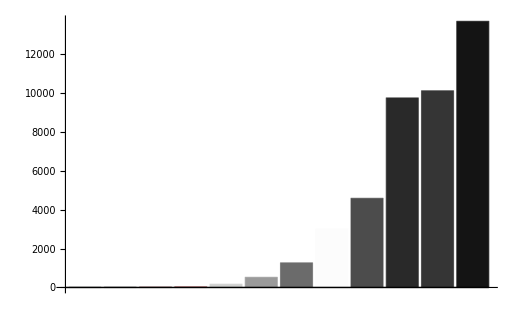

```mathematica
colorquantized=SortBy[Tally[Flatten[ImageData[ColorQuantize[-Graphics-,12,Dithering->False]],1]],Last];

BarChart[colorquantized[[All,2]],ChartStyle->RGBColor/@colorquantized[[All,1]]]
```

-Graphics-

{{{1.,0.843137,0.419608},4634},{{1.,0.721569,0.203922},10635},{{1.,0.929412,0.694118},13434},{{0.992157,0.592157,0.0980392},23300},{{0.866667,0.337255,0.184314},41939},{{0.980392,0.45098,0.0509804},56072},{{0.454902,0.160784,0.458824},70148},{{0.705882,0.235294,0.317647},71762},{{0.223529,0.0823529,0.301961},77949},{{0.,0.,0.},101299}}

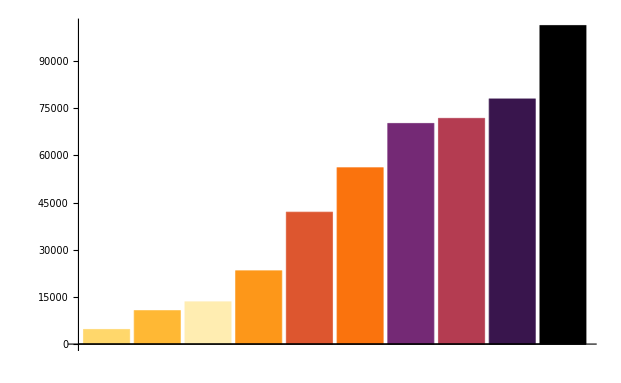

-Graphics-

```mathematica
img=-Graphics-(*-Graphics-*);


cl=ClusteringComponents[img,10];
im=Colorize[cl,ColorFunction->"SunsetColors"]

colorquantized=SortBy[Tally[Flatten[ImageData[ColorQuantize[im,10,Dithering->False]],1]],Last]
BarChart[colorquantized[[All,2]],ChartStyle->RGBColor/@colorquantized[[All,1]]]
ImageMultiply[im,img]
```

-Graphics-

{{{1.,0.941176,0.745098},2850},{{1.,0.882353,0.490196},7651},{{1.,0.784314,0.309804},13503},{{0.988235,0.568627,0.0901961},16416},{{1.,0.682353,0.129412},33231},{{0.980392,0.45098,0.0509804},35552},{{0.580392,0.196078,0.388235},41778},{{0.788235,0.258824,0.270588},52009},{{0.372549,0.137255,0.505882},57291},{{0.882353,0.356863,0.160784},57705},{{0.,0.,0.},67972},{{0.188235,0.0666667,0.254902},71642}}

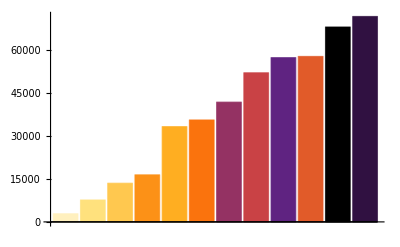

```mathematica
img=-Graphics-(**);


cl=ClusteringComponents[img,12];
im=Colorize[cl,ColorFunction->"SunsetColors"]

colorquantized=SortBy[Tally[Flatten[ImageData[ColorQuantize[im,12,Dithering->False]],1]],Last]
BarChart[colorquantized[[All,2]],ChartStyle->RGBColor/@colorquantized[[All,1]]]
```